# Avaliação silueta da torre cross-rope

## Inicialização

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\Usuário\Dropbox\TBE_calc_param\analise_tunico_cabos_ACSR\1700MVA\bonding_4_por_fase

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 16},ImageSize-> 600,Joined-> True,
PlotStyle-> {{Thick,Darker@Red},{Thick,Dashed,Darker@Blue},{Thick,DotDashed,Darker@Green},{Thick,Red,Dashed},{Thick,Green,Dashed},{Thick,Blue,Dashed}},
Axes-> False,Frame-> True];
```

```mathematica
<<nLCParam`
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

General::stop: Further output of CCompilerDriver`CreateLibrary :: nocomp will be suppressed during this calculation.

Compile::nogen: A library could not be generated from the compiled function.

General::stop: Further output of Compile :: nogen will be suppressed during this calculation.

```mathematica
hj=DateList[];
Print[hj[[3]],"/ ",hj[[2]],"/ ",hj[[1]]]
Print[" às ", hj[[4]], ":",hj[[5]]]
```

3/ 8/ 2018

às 15:27

## Dados dos Condutores

```mathematica
dadoscond=Import["condcompleta.txt","Table"];
camp=Import["campos.txt","CSV"];
```

### Dados do Meio

#### Ar

```mathematica
μ=4.0*Pi*10^-7;
ϵ=8.854 10^-12;
```

#### Solo

```mathematica
σs=10.0^-3;                                 (* ⟹ Condutividade do Solo ⟸ *)
```

### Dados do condutor

```mathematica
Nome=ToUpperCase["bittern"];
```

```mathematica
pos=Module[{posicao},posicao=If[NumberQ[Position[dadoscond,Nome][[1,1]]],Position[dadoscond,Nome][[1,1]],1];If[NumberQ[Position[dadoscond,Nome][[1,1]]],,Print["O condutor especificado não exite na tabela, verifique o nome digitado. Para não ocorrer erros nos cálculos foram utilizados os valores do condutor Owl"]];Return[posicao]];

{nome,MCM,NAl,DAl,NACO,DACO,secAl,secACO,Dcond,DALMA,PesoAl,PesoACO,Massa,CargaRupturaClasseA,CargaRupturaClasseB,Ampacidade,RMG,ResCC,ResAC,Xind,Xcap}=dadoscond[[pos]];

Table[Print[i,")  ",camp[[i,1]], " = ",dadoscond[[pos,i]]],{i,1,Length[camp]}];
```

Return[53]

1)  Nome comercial = BITTERN

2)  Bitola (MCM) = 1272

3)  Num. de Fios de Al. = 45

4)  Diâmetro dos Fios de Al. (mm) = 4.27

5)  Num. de Fios de Aço = 7

6)  Diâmetro dos Fios de Aço (mm) = 2.847

7)  Seção transversal de Al (mm^2) = 644.4

8)  Seção transversal do cond. (mm^2) = 689

9)  Diâmetro do cond. (mm) = 34.16

10)  Diâmetro da Alma de Aço (mm) = 8.54

11)  Peso Nominal do Al (aprox.) (kg/km) = 1785.4

12)  Peso nominal do Aço (aprox.) (kg/km) = 348.1

13)  Massa (aprox.) (kg/km) = 2133.4

14)  Carga de ruptura (Classe A) (kgf) = 15480

15)  Carga de ruptura (Classe B) (kgf) = 15175

16)  Ampacidade (A) = 1160

17)  Raio médio geométrico (m) = 0.01356

18)  Resistência elétrica máxima CC a 20.baC (Ohm/km) = 0.045

19)  Resistência elétrica máxima CA @ 60 Hz e 75.baC (Ohm/km) = 0.056

20)  Reatância indutiva (Ohm/km) = 0.3243

21)  Reatância capacitiva (Mohm/km) = 0.1943

### Dados dos Condutores

```mathematica
r0=(dadoscond[[pos,10]]/2)*10^-3;   (* ⟹ [m] ⟸ *)
r1=(dadoscond[[pos,9]]/2)*10^-3;

ρAl=0.028264;    (* resistividade ⟹ Ω × mm^2/ m ⟸ *)
ρAlmetro=0.028264*10^-6;    (* ⟹ Ω × m ⟸ *)

Rdcϕ=(dadoscond[[pos,18]])*10^-3;  (* ⟹ [Ω/m] ⟸⟹ @ 20^o ⟸*)
ρϕ=Rdcϕ*Pi*(r1^2-r0^2);

σϕ=(1/ρAlmetro)*(dadoscond[[pos,3]]*(dadoscond[[pos,4]]*10^-3/2)^2)/(r1^2-r0^2);
```

```mathematica
svao=0.55; (* comprimento do vão em [km] *)
T=dadoscond[[pos,15]];
W=dadoscond[[pos,13]];
H=0.24*T;
Ccat=H/W;
(*flecha em metro*)
flechacond=1000*Ccat*(Cosh[svao/(2*Ccat)]-1)
```

22.1976

### Dados dos Cabos PR

```mathematica
rpr=4.57*10^-3; (* [m] *)

Rdcpr=4.19*10^-3;

ρpr=Rdcpr*Pi*rpr^2;

σpr=1/ρpr;

μpr=80*μ;
```

```mathematica
Tpr=6980; (*{kgf]*)
Wpr=410; (*[kg/km]*)
Hpr=0.25*Tpr;
Ccatpr=Hpr/Wpr;
(*flecha em metro*)
flechapr=1000*Ccatpr*(Cosh[svao/(2*Ccatpr)]-1)
```

8.8874

## LT 500 kV

```mathematica
nfase=3;
nb=4;
npr=2;
ncond=nfase*nb+npr;
```

dados dos condutores obtidos a partir da saída do ATP, arquivo “RL-IBALM-101-900-MAT-008- C COORDISOL.PDF”. Contudo parece que há um erro numa altura. Foi feito a correção para q todos os feixes fiquem simétricos

```mathematica
coordcond=Import["LT_cabo_grackle.dat","Table"];
```

```mathematica
Dimensions[coordcond]
```

{2,14}

```mathematica
xc= coordcond[[1,All]];
yc= coordcond[[2,All]];
```

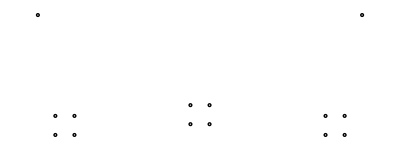

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->All,FrameTicks->{{-10,0,10},{5,15,25},False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

## Cálculo parâmetros sequência

```mathematica
a=Exp[I 120 Degree];
A={{1.,1.,1.},{1.,a^2,a},{1.,a,a^2}};
```

```mathematica
(* cenario 1: com pr e com feixe nas fases *)
{Z,Y}= calcZYlt[2 π 60., xc,yc,σs, Rdcϕ, r1, r0, 2, Rdcpr, rpr, nb] ;
```

```mathematica
seqZ=Diagonal[Inverse[A].Z.A];
seqY=Diagonal[Inverse[A].Y.A];
```

```mathematica
seqZ 1000.0
```

{0.188448+1.43104 ⅈ,0.011771+0.249683 ⅈ,0.011771+0.249683 ⅈ}

```mathematica
Pn=500.^2/Sqrt[seqZ[[2]]/seqY[[2]] ]
```

1307.91+30.526 ⅈ

## Avaliação de potência natural e reatância em função da distância

```mathematica
h={-5,0, 5, 10, 15, 100};
x1=pn=Table[0.,{Length[h]}];
Do[{h0=h[[nm]];
{Z,Y}= calcZYlt[2 π 60., xc,h0+yc,σs, Rdcϕ, r1, r0, 2, Rdcpr, rpr, nb] ;
seqZ=Diagonal[Inverse[A].Z.A];
seqY=Diagonal[Inverse[A].Y.A];
x1[[nm]]=Im[seqZ[[2]]] 1000.0;
pn[[nm]]=Re[500.^2/Sqrt[seqZ[[2]]/seqY[[2]] ]]
},{nm,1,Length[h]}]
```

```mathematica
N[x1,12]
```

{0.249683,0.249683,0.249683,0.249683,0.249683,0.249683}

```mathematica
pn
```

{1321.48,1307.91,1301.9,1298.75,1296.9,1292.31}